## Problem 1

Here, we expand the dispersion relation around  for part d.

```mathematica
Series[k/Sqrt[k^2+1],{k,0,3}]
```

k-k^3/2+O[k]^4

## Problem 2

We define our ansatz and plug it into our PDE.

```mathematica
a[x_,t_]=Exp[I*Integrate[V[x,t],x]]*Sqrt[ρ[x,t]];
```

```mathematica
Simplify[I*D[a[x,t],t]+D[a[x,t],{x,2}]-Abs[a[x,t]]^2*a[x,t],Assumptions->{{Integrate[V[x,t],x]}∈Reals,ρ[x,t]>=0}]
```

-1/(4 ρ[x,t]^(3/2))ⅇ^(ⅈ ∫V[x,t]ⅆx) (4 (∫V^(0,1)[x,t]ⅆx) ρ[x,t]^2+4 V[x,t]^2 ρ[x,t]^2+4 ρ[x,t]^3-2 ⅈ ρ[x,t] ρ^(0,1)[x,t]-4 ⅈ ρ[x,t]^2 V^(1,0)[x,t]-4 ⅈ V[x,t] ρ[x,t] ρ^(1,0)[x,t]+(ρ^(1,0)[x,t])^2-2 ρ[x,t] ρ^(2,0)[x,t])

Here, we differentiate the equation given by the real part.

```mathematica
real[x,t]=-ρ[x,t]-V[x,t]^2-(Derivative[1,0][ρ][x,t]/(2ρ[x,t]))^2+Derivative[2,0][ρ][x,t]/(2 ρ[x,t] );
```

```mathematica
D[real[x,t],x]
```

-2 V[x,t] V^(1,0)[x,t]-ρ^(1,0)[x,t]+((ρ^(1,0)[x,t])^3)/(2 ρ[x,t]^3)-(ρ^(1,0)[x,t] ρ^(2,0)[x,t])/ρ[x,t]^2+(ρ^(3,0)[x,t])/(2 ρ[x,t])

Here, we expand the dispersion relation in a series around .

```mathematica
Series[k*Sqrt[k^2+2],{k,0,3}]
```

√2 k+k^3/(2 √2)+O[k]^4

## Problem 3

We plug the same ansatz into our new equation and get the following.

```mathematica
Simplify[I*D[a[x,t],t]+D[a[x,t],{x,2}]+Abs[a[x,t]]^2*a[x,t],Assumptions->{{Integrate[V[x,t],x]}∈Reals,ρ[x,t]>=0}]
```

1/(4 ρ[x,t]^(3/2))ⅇ^(ⅈ ∫V[x,t]ⅆx) (-4 (∫V^(0,1)[x,t]ⅆx) ρ[x,t]^2-4 V[x,t]^2 ρ[x,t]^2+4 ρ[x,t]^3+2 ⅈ ρ[x,t] ρ^(0,1)[x,t]+4 ⅈ ρ[x,t]^2 V^(1,0)[x,t]+4 ⅈ V[x,t] ρ[x,t] ρ^(1,0)[x,t]-(ρ^(1,0)[x,t])^2+2 ρ[x,t] ρ^(2,0)[x,t])

Observe that the series has imaginary coefficients around .

```mathematica
Series[k*Sqrt[k^2-2],{k,0,3}]
```

Piecewise[{{-ⅈ √2 k+(ⅈ k^3)/(2 √2)+O[k]^4, Im[k^2]<0}, {ⅈ √2 k-(ⅈ k^3)/(2 √2)+O[k]^4, True}}]

## Problem 4

```mathematica
α=1; v=1.5;
```

```mathematica
Plot[-U^4/2+2v*U^2+α*U,{U,-3,3}]
```

We let the red line denote  and the green line denote .

```mathematica
α=0; v=1.5;
```

```mathematica
Plot[-U^4/2+2v*U^2+α*U,{U,-3,3}]
```

Note that  causes both local maxima to be equivalent, i.e., .

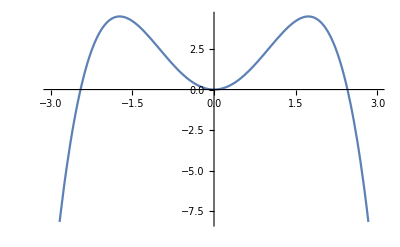

Case 1: , so we have a single equilibrium point. We produce plots for both  normalized and the special case .

```mathematica
α=1; v=3/(4*CubeRoot[2])-0.3;
```

```mathematica
StreamPlot[{u2,2u1^3-4v*u1-α},{u1,-3,3},{u2,-3,3}]
```

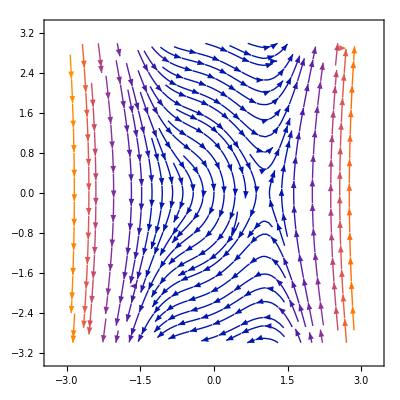

```mathematica
α=0; v=-1;
```

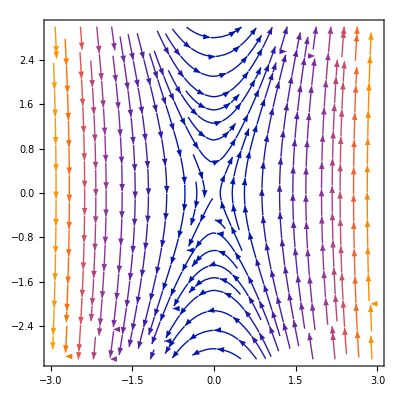

```mathematica
StreamPlot[{u2,2u1^3-4v*u1-α},{u1,-3,3},{u2,-3,3}]
```

In these, we observe a single unstable equilibrium point.

Case 2: , so we have a potentially degenerate equilibrium point.

```mathematica
α=1; v=3/(4*CubeRoot[2]);
```

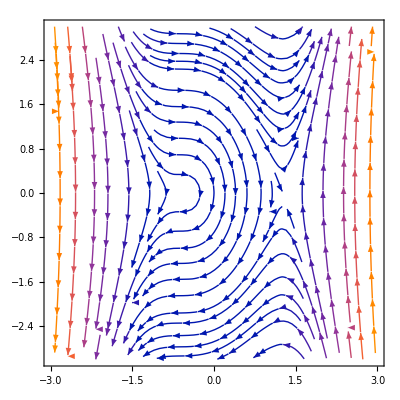

```mathematica
StreamPlot[{u2,2u1^3-4v*u1-α},{u1,-3,3},{u2,-3,3}]
```

As expected, we observe a degenerate equilibrium point here in addition to the unstable point from before.

```mathematica
α=0; v=0;
```

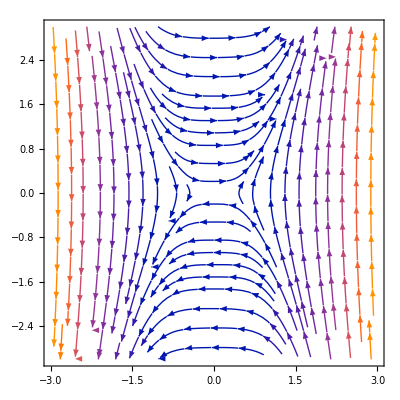

```mathematica
StreamPlot[{u2,2u1^3-4v*u1-α},{u1,-3,3},{u2,-3,3}]
```

Note that our the equilibrium points appear to have coalesced.

Case 3: , so we have 3 equilibrium points.

```mathematica
α=1; v=3/(4*CubeRoot[2])+0.3;
```

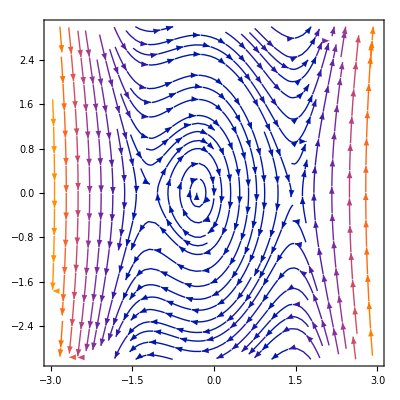

```mathematica
StreamPlot[{u2,2u1^3-4v*u1-α},{u1,-3,3},{u2,-3,3}]
```

Here, we see an homoclinic orbit separate from our unstable point from earlier.

```mathematica
α=0; v=3/(4*CubeRoot[2])+0.3;
```

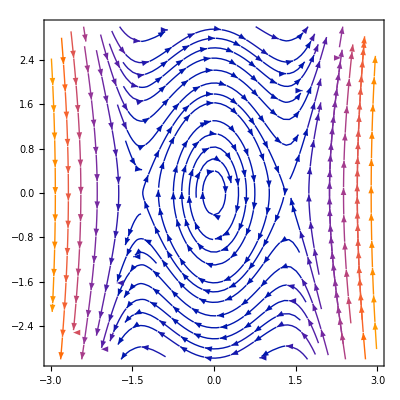

```mathematica
StreamPlot[{u2,2u1^3-4v*u1-α},{u1,-3,3},{u2,-3,3}]
```

In the  case, we instead see a heteroclinic orbit.

```mathematica
Clear[v]
```

```mathematica
Integrate[1/Sqrt[2(2v^2+U^4/2-2v*U^2)],U]
```

-((U^2-2 v) ArcTanh[U/(√2 √v)])/(√2 √((U^2-2 v)^2) √v)

## Problem 5

```mathematica
Clear[α]
```

```mathematica
b[x_,t_]=B[x,t]*Exp[I*θ[x,t]];
```

```mathematica
Simplify[D[b[x,t],t]+α*D[b[x,t]*B[x,t]^2,x]-I*D[b[x,t],{x,2}],Assumptions->{B[x,t],θ[x,t]}∈Reals]
```

ⅇ^(ⅈ θ[x,t]) (B^(0,1)[x,t]+3 α B[x,t]^2 B^(1,0)[x,t]+ⅈ α B[x,t]^3 θ^(1,0)[x,t]+2 B^(1,0)[x,t] θ^(1,0)[x,t]-ⅈ B^(2,0)[x,t]+B[x,t] (ⅈ θ^(0,1)[x,t]+ⅈ (θ^(1,0)[x,t])^2+θ^(2,0)[x,t]))

We expand and collect terms in part d here.

```mathematica
Collect[(C+v*s-3s^2)-v*(C+v*s-3s^2)/(2s)-ω+((C+v*s-3s^2)/(2s))^2,s]
```

-C/2+C^2/(4 s^2)-(3 s^2)/4+s v-v^2/4-ω

```mathematica
Collect[Integrate[(C+v*s-3s^2)-v*(C+v*s-3s^2)/(2s)-ω+((C+v*s-3s^2)/(2s))^2,s],s]
```

-C^2/(4 s)-s^3/4+(s^2 v)/2+1/4 s (-2 C-v^2-4 ω)